## Harvest fold - Compare reliability of variance and Smax

Simulate May’s harvesting model close and far from the fold bifurcation (fixed bifurcation parameter)
Record EWS over multiple simulations (far and close to fold bifurcation)
Plot pdfs of EWS
Do this for a different times-series lengths
Do the same thing for different types of noise in the model

## Setup and Universal Parameters

```mathematica
SetDirectory["/Users/tb460/Library/Mobile Documents/com~apple~CloudDocs/Research/critical_transitions_16/fold_harvest/multiplicative_noise"];
```

```mathematica
(* Good fonts *)
TMBFS10={FontFamily->"Helvetica",FontSize->10};
TMBFS12={FontFamily->"Helvetica",FontSize->12};
TMBFS15={FontFamily->"Helvetica",FontSize->15};
TMBbold={FontFamily->"Helvetica",FontSize->15,Bold};
(* Neat colours *)
TMBcolours=ColorData[97,"ColorList"]
```

{RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.880722, 0.611041, 0.142051],RGBColor[0.560181, 0.691569, 0.194885],RGBColor[0.922526, 0.385626, 0.209179],RGBColor[0.528488, 0.470624, 0.701351],RGBColor[0.772079, 0.431554, 0.102387],RGBColor[0.363898, 0.618501, 0.782349],RGBColor[1, 0.75, 0],RGBColor[0.647624, 0.37816, 0.614037],RGBColor[0.571589, 0.586483, 0.],RGBColor[0.915, 0.3325, 0.2125],RGBColor[0.40082222609352647, 0.5220066643438841, 0.85],RGBColor[0.9728288904374106, 0.621644452187053, 0.07336199581899142],RGBColor[0.736782672705901, 0.358, 0.5030266573755369],RGBColor[0.28026441037696703, 0.715, 0.4292089322474965]}

```mathematica
(* get packages for user-defined functions *)
Get["/Users/tb460/Library/Mobile Documents/com~apple~CloudDocs/Mathematica/mma_functions/ews_spec.wl"];

Get["/Users/tb460/Library/Mobile Documents/com~apple~CloudDocs/Mathematica/mma_functions/ews_std.wl"];
```

```mathematica
(* Universal simulation parameters *)
dt=0.1; (* time step for stochastic simulation *)
dt2 = 1; (* time separation for indicator calculation - increase to speed up computation *)
tmax=100; (* time units in simulation *)
numSims=1000; (* number of realisations to average over *)

(* options for EWS calculation *)
detrendOp=1; (* 1 for yes, 0 for no *)
bandWidth=0.2; (* for Gaussian filtering (as a percentage) *)
rollWindow=0.25;(* for indicator calculation *)
toffset=0; (* time before bifurcation point to stop evaluating EWS *)

(* hamming window size and length *)
hamLength=10; 
hamOffset=5; 


(* lag autocorrelation *)
numComps=tmax/dt+1; (* number of components in simulation *)
tauVals={1};

(* Figure display parameters *)
aHeadSize=0.03;
{padLeft,padRight,padBottom,padTop}={60,50,20,20};  (* image padding *)
indexPos=Scaled[{0.065,1.10}]; (* scaled position of base index *)
labelPos=Scaled[{1.05,-0.1}]; (* scaled position of x label *)
arHeight=0.15; (* height of rolling window arrow *)
labelLetterPos={0.035,0.86} ;(* panel letter label *)
```

## Model Analysis

```mathematica
(* Clear variable names *)
Clear[f,x,r,h,s,k]
$Assumptions={x,r,s,k}∈Reals;
```

```mathematica
(* Dynamic equations *)
f[x_]:=r x(1-x/k) - h x^2/(s^2+x^2);
```

```mathematica
f[x]
```

r x (1-x/k)-(h x^2)/(s^2+x^2)

```mathematica
(* Parameter values *)
r=1;
k=1;
s=0.1;
```

```mathematica
(* Find equilibiria *)
equi=Solve[f[x]==0,x]//Quiet;
```

```mathematica
equi/.{h->0.1}
```

{{x→0.},{x→0.0555458+0.0903572 ⅈ},{x→0.888908+0. ⅈ},{x→0.0555458-0.0903572 ⅈ}}

```mathematica
(* Initial stable equilibrium *)
equiInit=Re[x/.equi[[3]]];

(* Bifurcation point *)
{xbif,hbif}=Re[{x,h}/.Solve[f[x]==0&&f'[x]==0][[3]]]//Quiet
```

{0.478128,0.260437}

```mathematica
(* Eigenvalue at equilibrium point *)
Clear[λ]
λ[a_]=D[f[x],x]/.{x->equiInit};
```

```mathematica
(* Phase portrait, hval control parameter *)
Manipulate[
Plot[f[x]/.{r->rval,h->hval,s->sval},{x,0,1},
PlotRange->{-0.2,0.2},
AxesLabel->{"x","f(x)"},
LabelStyle->TMBFS12],
{{rval,1},0.5,1.5},{{hval,0},0,0.4},{{sval,0.1},0.05,0.3}];
```

## Stochastic Simulation

Stochastic model 
dX = rX(1-X/K) -hX^2/(s^2+X^2)

```mathematica
hbif
```

0.260437

### Key parameters

```mathematica
a1=0.01;(* noise intensity *)
r=1; (* model parameteres *)
s=0.1;
k=1;
hl=0.15; (* h value far from bifurcation *)
hh=0.24; (* h value close to bifurcation *)
seed=10; (* seed number *)
numComps=tmax/dt+1; (* number of components in time-series *)

(* choose an h value to run simulations at *)
hchoice=hl;
```

```mathematica
x0=equiInit/.h->hchoice; (* initial condition *)
```

### Model Dynamics

```mathematica
Clear[f]
f[x_,r_,s_,k_,h_]:=r x(1-x/k)-h x^2/(s^2+x^2);
```

### Stochastic Simulation Setup

```mathematica
(* clear function labels *)
Clear[stochProc,stochSol,stochData]
```

```mathematica
(* fixed control parameter *)
Clear[h,t]
h[t_]:=hchoice
```

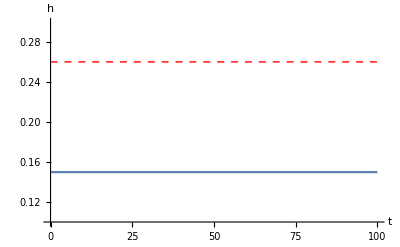

```mathematica
(* h plot *)
hPlot=Plot[{h[t],hbif},{t,0,tmax},
LabelStyle->14,
AxesLabel->{"t","h"},
PlotStyle->{Automatic,{Dashed,Thick,Red}},
PlotRange->{{0,tmax},{0.1,0.3}}]
```

```mathematica
(* number of components in simulation *)
nComps=Floor[tmax/dt]+1;
```

```mathematica
(* array for output time-series *)
t=Range[0,tmax,dt];
xr=ConstantArray[0,{numSims,nComps}]; (* x values with noise to r *)
xk=ConstantArray[0,{numSims,nComps}]; (* x values with noise to k *)
xs=ConstantArray[0,{numSims,nComps}]; (* x values with noise to s *)
xAdd=ConstantArray[0,{numSims,nComps}]; (* x values with additive noise to state *)
xMulti=ConstantArray[0,{numSims,nComps}]; (* x values with mutliplicative noise proportional to state *)
```

```mathematica
(* intitial condition *)
xr[[;;,1]]=x0;
xk[[;;,1]]=x0;
xs[[;;,1]]=x0;
xAdd[[;;,1]]=x0;
xMulti[[;;,1]]=x0;
```

### Noise set up

```mathematica
(* noise amplitudes for parameters *)
rAmp=0.1; (* as proportion of parameter *)
kAmp=0.1;
sAmp=0.1;
addAmp=a1;
multiAmp=a1;
```

```mathematica
(* noisy parameter values *)
rNoise=r+rAmp*RandomVariate[NormalDistribution[0,1],{numSims,nComps}];
kNoise=k+kAmp*RandomVariate[NormalDistribution[0,1],{numSims,nComps}];
sNoise=s+sAmp*RandomVariate[NormalDistribution[0,1],{numSims,nComps}];
```

```mathematica
(* multiplicative state noise values *)
multiStateNoise=Sqrt[dt]*multiAmp*RandomVariate[NormalDistribution[0,1],{numSims,nComps}];

(* additive state noise values *)
addStateNoise=Sqrt[dt]*addAmp*RandomVariate[NormalDistribution[0,1],{numSims,nComps}];
```

### Simulations

```mathematica
f[x_,r_,s_,k_,h_]:=r x(1-x/k)-h x^2/(s^2+x^2);
```

#### Noise on r

```mathematica
(* set up counter *)
For[j=1,j≤numSims,j++,
For[i=1,i≤nComps-1,i++,
(* update state variable *)
xr[[j,i+1]]=xr[[j,i]]+f[xr[[j,i]],rNoise[[j,i]],s,k,h[t[[i]]]]dt;
(* make sure state variable stays above x=0 *)
If[xr[[j,i+1]]≤0,xr[[j,i+1]]=0];
]
]
```

#### Noise on K

```mathematica
(* set up counter *)
For[j=1,j≤numSims,j++,
For[i=1,i≤nComps-1,i++,
(* update state variable *)
xk[[j,i+1]]=xk[[j,i]]+f[xk[[j,i]],r,s,kNoise[[j,i]],h[t[[i]]]]dt;
(* make sure state variable stays above x=0 *)
If[xk[[j,i+1]]≤0,xk[[j,i+1]]=0];
]
]
```

#### Noise on s

```mathematica
(* set up counter *)
For[j=1,j≤numSims,j++,
For[i=1,i≤nComps-1,i++,
(* update state variable *)
xs[[j,i+1]]=xs[[j,i]]+f[xs[[j,i]],r,sNoise[[j,i]],k,h[t[[i]]]]dt;
(* make sure state variable stays above x=0 *)
If[xs[[j,i+1]]≤0,xs[[j,i+1]]=0];
]
]
```

#### Additive noise to state

```mathematica
(* set up counter *)
For[j=1,j≤numSims,j++,
For[i=1,i≤nComps-1,i++,
(* update state variable *)
xAdd[[j,i+1]]=xAdd[[j,i]]+f[xAdd[[j,i]],r,s,k,h[t[[i]]]]dt +addStateNoise[[j,i]] ;
(* make sure state variable stays above x=0 *)
If[xAdd[[j,i+1]]≤0,xAdd[[j,i+1]]=0];
]
]
```

#### Multiplicative noise to state

```mathematica
(* set up counter *)
For[j=1,j≤numSims,j++,
For[i=1,i≤nComps-1,i++,
(* update state variable *)
xMulti[[j,i+1]]=xMulti[[j,i]]+f[xMulti[[j,i]],r,s,k,h[t[[i]]]]dt+xMulti[[j,i]]*multiStateNoise[[j,i]] ;
(* make sure state variable stays above x=0 *)
If[xMulti[[j,i+1]]≤0,xMulti[[j,i+1]]=0];
]
]
```

#### Coarsen time-series for computational speed

```mathematica
tCrs=t[[1;;-1;;Floor[dt2/dt]]];
xrCrs=xr[[;;,1;;-1;;Floor[dt2/dt]]];
xsCrs=xs[[;;,1;;-1;;Floor[dt2/dt]]];
xkCrs=xk[[;;,1;;-1;;Floor[dt2/dt]]];
xAddCrs=xAdd[[;;,1;;-1;;Floor[dt2/dt]]];
xMultiCrs=xMulti[[;;,1;;-1;;Floor[dt2/dt]]];
```

## Traditional EWS

### Detrend time-series

```mathematica
resR=Table[xrCrs[[i]]-TBdetrend[Transpose[{tCrs,xrCrs[[i]]}],bandWidth][[;;,2]],{i,1,numSims}];
```

```mathematica
resR//Dimensions
```

{1000,101}

```mathematica
resR=Table[xrCrs[[i]]-TBdetrend[Transpose[{tCrs,xrCrs[[i]]}],bandWidth][[;;,2]],{i,1,numSims}];
resS=Table[xsCrs[[i]]-TBdetrend[Transpose[{tCrs,xsCrs[[i]]}],bandWidth][[;;,2]],{i,1,numSims}];
resK=Table[xkCrs[[i]]-TBdetrend[Transpose[{tCrs,xkCrs[[i]]}],bandWidth][[;;,2]],{i,1,numSims}];
resAdd=Table[xAddCrs[[i]]-TBdetrend[Transpose[{tCrs,xAddCrs[[i]]}],bandWidth][[;;,2]],{i,1,numSims}];
resMulti=Table[xMultiCrs[[i]]-TBdetrend[Transpose[{tCrs,xMultiCrs[[i]]}],bandWidth][[;;,2]],{i,1,numSims}];
```

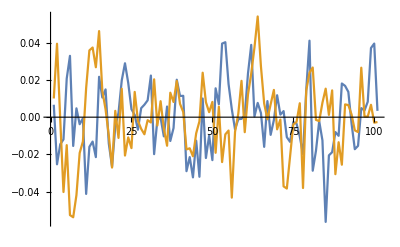

```mathematica
ListLinePlot[resK[[1;;2]]]
```

```mathematica
resR//Dimensions
```

{1000,101}

### Compute EWS

```mathematica
(* noise in r *)
varianceR=Table[Variance[resR[[i]]],{i,1,numSims}];
acR=Table[CorrelationFunction[resR[[i]],1],{i,1,numSims}];

(* noise in s *)
varianceS=Table[Variance[resS[[i]]],{i,1,numSims}];
acS=Table[CorrelationFunction[resS[[i]],1],{i,1,numSims}];

(* noise in K *)
varianceK=Table[Variance[resK[[i]]],{i,1,numSims}];
acK=Table[CorrelationFunction[resK[[i]],1],{i,1,numSims}];

(* additive noise *)
varianceAdd=Table[Variance[resAdd[[i]]],{i,1,numSims}];
acAdd=Table[CorrelationFunction[resAdd[[i]],1],{i,1,numSims}];

(* state dependent noise *)
varianceMulti=Table[Variance[resMulti[[i]]],{i,1,numSims}];
acMulti=Table[CorrelationFunction[resMulti[[i]],1],{i,1,numSims}];
```

```mathematica
varData={varianceR,varianceS,varianceK,varianceAdd,varianceMulti};
acData={acR,acS,acK,acAdd,acMulti};
```

```mathematica
(* export variance data *)
Export["data_export/varDataFar100.csv",varData];
(* export ac data *)
Export["data_export/acDataFar100.csv",acData];
```

## Power Spectrum EWS

```mathematica
resR//Dimensions
```

{1000,101}

### Compute power spectrum with Hamming window

```mathematica
?TBPowerSpecWelch
```

{freqVals,pSpec} = TBPowerSpecWelch[{yVals,dt,hamLength,hamOffset,wProp_:1}] estimates the power spectrum usign Welch's method.
This involves computing the periodogram with overlapping Hamming windows.
hamLength: number of data points in Hamming window, or if in (0,1) taken as a proportion of total data input
hamOffset: number of data points to offset the window by on each interation, or if in (0,1) taken as a proportion of Hamming window size
wProp: optional argument of proportion of frequency values to go up to (can cutoff higher frequencies if necesssary)

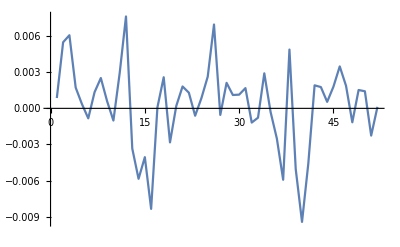

```mathematica
ListLinePlot[resR[[1,transTime;;]]]
```

```mathematica
transTime
```

50

```mathematica
(* evaluate power spectrum of residuals in rolling window with the offset the same as hamOffset *)
pSpecSeriesR=Table[TBPowerSpecWelch[{resR[[i]],dt2,hamLength,hamOffset}],{i,1,numSims}];
pSpecSeriesK=Table[TBPowerSpecWelch[{resK[[i]],dt2,hamLength,hamOffset}],{i,1,numSims}];
pSpecSeriesS=Table[TBPowerSpecWelch[{resS[[i]],dt2,hamLength,hamOffset}],{i,1,numSims}];
pSpecSeriesAdd=Table[TBPowerSpecWelch[{resAdd[[i]],dt2,hamLength,hamOffset}],{i,1,numSims}];
pSpecSeriesMulti=Table[TBPowerSpecWelch[{resMulti[[i]],dt2,hamLength,hamOffset}],{i,1,numSims}];
```

```mathematica
(* frequncy values of power spectra *)
ωVals=pSpecSeriesR[[1,1,1]];
```

### Compute Smax

```mathematica
(* Subscript[S, max] data *)
specMaxR=Table[Max[pSpecSeriesR[[i,2,;;]]],{i,1,numSims}];
specMaxS=Table[Max[pSpecSeriesS[[i,2,;;]]],{i,1,numSims}];specMaxK=Table[Max[pSpecSeriesK[[i,2,;;]]],{i,1,numSims}];specMaxAdd=Table[Max[pSpecSeriesAdd[[i,2,;;]]],{i,1,numSims}];specMaxMulti=Table[Max[pSpecSeriesMulti[[i,2,;;]]],{i,1,numSims}];
```

```mathematica
smaxData={specMaxR,specMaxS,specMaxK,specMaxAdd,specMaxMulti};
```

```mathematica
(* export smax data *)
Export["data_export/smaxDataFar100.csv",smaxData];
```

## Distribution plots of EWS

```mathematica
(* import data *)
varDataNear=Import["data_export/varDataNear100.csv"];
varDataFar=Import["data_export/varDataFar100.csv"];

acDataNear=Import["data_export/acDataNear100.csv"];
acDataFar=Import["data_export/acDataFar100.csv"];
```

```mathematica
smaxDataNear=Import["data_export/smaxDataNear100.csv"];
smaxDataFar=Import["data_export/smaxDataFar100.csv"];
```

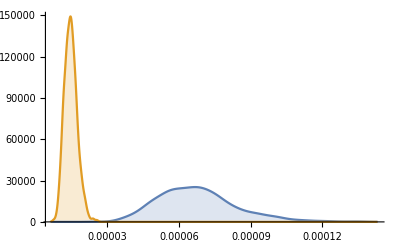
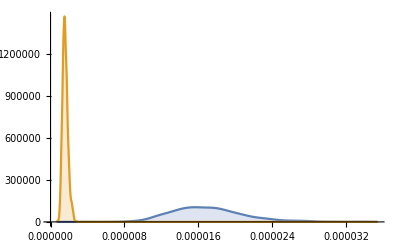
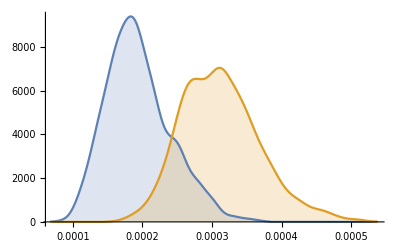
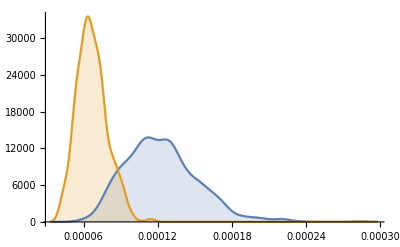
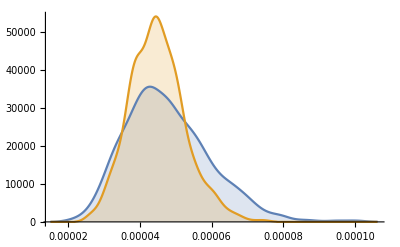

```mathematica
Table[SmoothHistogram[{varDataNear[[i]],varDataFar[[i]]},Automatic,"PDF",PlotRange->All,Filling->Bottom],{i,1,5}]
```

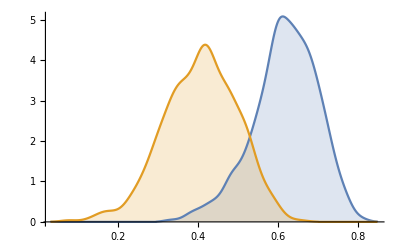
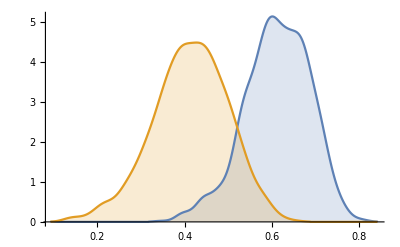
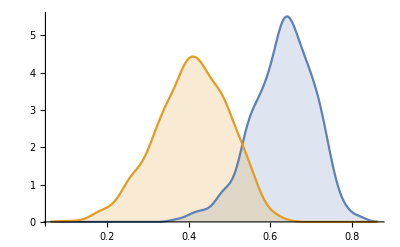
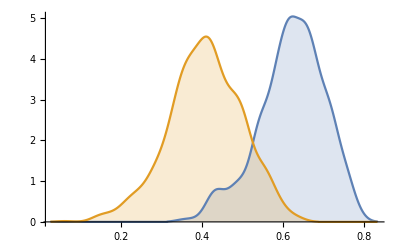
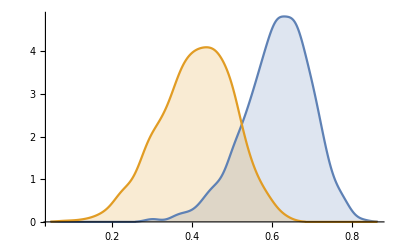

```mathematica
Table[SmoothHistogram[{acDataNear[[i]],acDataFar[[i]]},Automatic,"PDF",PlotRange->All,Filling->Bottom],{i,1,5}]
```

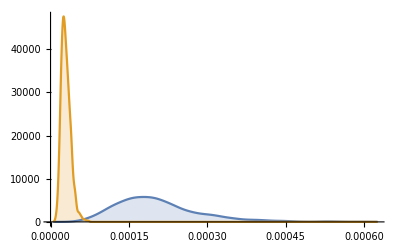
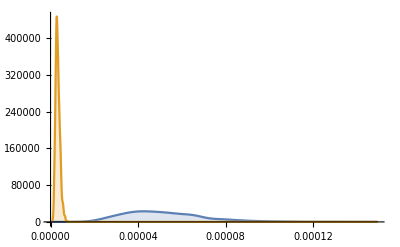
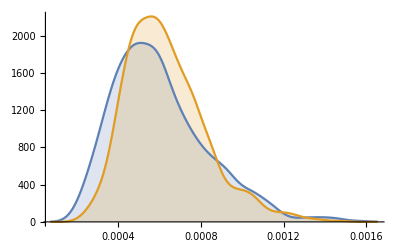
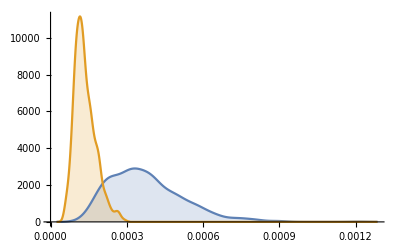
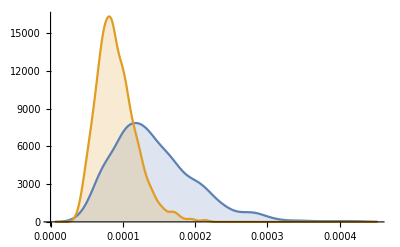

```mathematica
Table[SmoothHistogram[{smaxDataNear[[i]],smaxDataFar[[i]]},Automatic,"PDF",PlotRange->All,Filling->Bottom],{i,1,5}]
```